```mathematica
Clear["Global`*"];
lagrangian[T_,V_,Q_:0,genCoords_List] :=
	Module[{L=T-V},
	(D[D[L,D[#,t]],t] == Q + D[L,#])& /@ genCoords
	];

xl[t_]= X[t] + (d - (l[t]- h) Tan [theta[t]]) Cos [theta[t]];
yl[t_]= y[t] + (l[t] - h) Cos[theta[t]] + d Sin[theta[t]];

xw[t_]= X[t] - (dw -d) Cos[theta[t]];
yw[t_]= y[t] -(dw -d) Sin[theta[t]];

xp[t_]= X[t] + d Cos[theta[t]];
yp[t_]= y[t] + d Sin[theta[t]];

genCoords = {X[t], y[t], l[t], theta[t], phi[t]};

T = 1/2 mw (xw'[t]^2 + yw'[t]^2) +  1/2 mp (xp'[t]^2 + yp'[t]^2) +  1/2 ml (xl'[t]^2 + yl'[t]^2) + 1/2 Iw (phi'[t] + theta'[t])^2 + 1/2 Ib theta'[t]^2;
V = g(ml yl[t] + mw yw[t] + mp yp[t]) + 1/2 K (l[t] - l0)^2;
Q = 0;

eq = lagrangian[T, V, Q, genCoords] //Simplify;

hopHeight = 1;
horizVel = 1;

initialConditions = { X[0] == 0, y[0] == 1, l[0] == 0.3, theta[0] ==  0, phi[0] == 0, X'[0]== horizVel, y'[0]== 0, l'[0] == 0, theta'[0] == 0, phi'[0] == 0};
eq = Join[eq, initialConditions];
values = {mw -> 1.5, mp -> 2.5, ml -> 0.7, Iw -> 1.5*0.6*0.6/2, Ib -> 0.5, K -> 500, l0 -> 0.3, h -> 0.3, d-> 0.1, dw -> 0.2, g-> 9.8, L-> 0.5};
eqNum = eq /. values;
```

start : 0   end : 0.404061 [s]

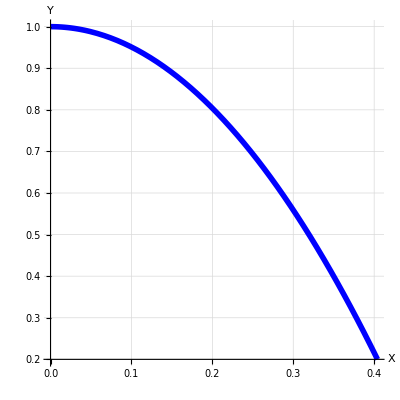

```mathematica
start = 0;
solveFor = {X, y, l, theta, phi};
sol = First[NDSolve[eqNum, solveFor, {t, 0,1}, Method -> {"EventLocator", "Event" -> y[t] - Cos[theta[t]](0.5 - l[t] - 0.1 Sin[theta[t]]), "EventAction" :> Throw[end = t, "StopIntegration"]}]];

Print ["start : " , start, "   end : ", end, " [s]"]
ParametricPlot[Evaluate[{X[t], y[t]} /. sol], {t, start, end}, AxesLabel -> {X, Y}, LabelStyle -> Directive[Black, Bold], PlotStyle -> {Blue, Thickness[0.01]},GridLines -> Automatic, GridLinesStyle -> Directive[Dashed], AspectRatio -> 1 ]
```

```mathematica
theta'[end] /. sol
```

7.05555×10^-15